I don’t understand why, but sympy’s Taylor-series expansions of inverse polynomials get painfully slow for polynomial orders above about 10, becoming exponentially slower for higher orders, and completely impractical (taking days and huge amounts of memory) much above 13 or so.  Mathematica, on the other hand, can do the same expansions in roughly a second.

These expansions are necessary for, e.g., TaylorT4 and T5.  (Though the large orders measured below are not generally necessary.)

{{1,0.0006},{2,0.00105},{3,0.00191},{4,0.00323},{5,0.00877},{6,0.01495},{7,0.0244},{8,0.03847},{9,0.0601},{10,0.00255},{11,0.00255},{12,0.009594},{13,0.00257},{14,0.01235},{15,0.01519},{16,0.0496},{17,0.07239},{18,0.11072},{19,0.16172},{20,0.23365},{21,0.32885},{22,0.45098},{23,0.6065},{24,0.77504},{25,0.987919},{26,1.23265},{27,1.52246},{28,1.85424},{29,2.24559},{30,2.68337},{31,3.18354},{32,4.88563},{33,8.26091},{34,13.17179},{35,20.61707},{36,32.65597},{37,47.80813},{38,63.63806},{39,82.63282},{40,107.34439}}

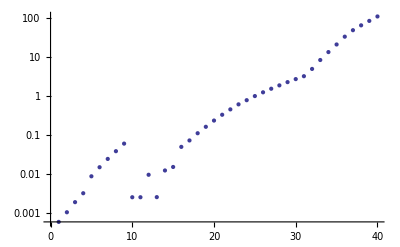

```mathematica
Timings = {};
For[PNOrder = 1,
PNOrder≤40,
PNOrder++,
A = Sum[a[i] v^i,{i,0,PNOrder}];
B = Sum[b[i] v^i,{i,0,PNOrder}];
AppendTo[Timings,{PNOrder,Timing[Series[A/B,{v,0,PNOrder}];][[1]]}];
]
Print[Timings]
ListLogPlot[Timings]
```